```mathematica
<<NumericalDifferentialEquationAnalysis`
(*IntegrationRule[N_]:=Block[{pts,w,npts},
{pts,w}=Transpose[GaussianQuadratureWeights[N+1,-1,1]];
npts=Length[pts];
Flatten[Table[{pts[[j]],pts[[i]],w[[j]]w[[i]]},{i,npts,1,-1},{j,1,npts}],1]
]*)
```

```mathematica
(*Retorna os pontos e os pesos da regra de integração  - order = ordem polinomial das funções de base  eltype = 1 quadrilátero 2 triângulo*)
IntegrationRule[order_,eltype_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},

If[eltype==1,
If[order==1,
matpsts={{-0.5773502691896257,0.5773502691896257,1.},{0.5773502691896257,0.5773502691896257,1.},{-0.5773502691896257,-0.5773502691896257,1.},{0.5773502691896257,-0.5773502691896257,1.}};
];
If[order==2,
matpsts={{-0.7745966692414834,0.7745966692414834,0.30864197530864174},{0.,0.7745966692414834,0.4938271604938271},{0.7745966692414834,0.7745966692414834,0.30864197530864174},{-0.7745966692414834,0.,0.4938271604938271},{0.,0.,0.7901234567901237},{0.7745966692414834,0.,0.4938271604938271},{-0.7745966692414834,-0.7745966692414834,0.30864197530864174},{0.,-0.7745966692414834,0.4938271604938271},{0.7745966692414834,-0.7745966692414834,0.30864197530864174}};
];
,
If[order==1,
matpsts=N[{{1/3,1/3,1/2}}];
];
If[order==2,
matpsts=N[{{1/6,1/6,1/2 1/3},{2/3,1/6,1/2 1/3},{1/6,2/3,1/2 1/3}}];
];

If[order==3,
matpsts=N[{{1/3,1/3,-27/48 1/2},{1/5,1/5,25/48 1/2},{1/5,3/5,25/48 1/2},{3/5,1/5,25/48 1/2}}];
];

];
matpsts//N
]
```

```mathematica
(*Calcula as funções de forma e as derivadas de triângulos e quadriláteros*)
Compute2DShape[order_,eltype_]:=Block[{ζ1,ζ2,ζ3,a,b,xi,eta,psis,dpsis},

If[eltype==1,
(*Quad*)
If[order==1,

psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
dpsis={{-0.250 (1.0-1.0 eta),0.250 (1.0-1.0 eta),0.250 (1.0+eta),-0.250 (1.0+eta)},{-0.250 (1.0-1.0 xi),-0.250 (1.0+xi),0.250 (1.0+xi),0.250 (1.0-1.0 xi)}};
];
If[order==2,

psis={xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)};
dpsis={{0.250 (-1.0+eta) eta (-1.0+xi)+0.250 (-1.0+eta) eta xi,0.250 (-1.0+eta) eta xi+0.250 (-1.0+eta) eta (1.0+xi),0.250 eta (1.0+eta) xi+0.250 eta (1.0+eta) (1.0+xi),0.250 eta (1.0+eta) (-1.0+xi)+0.250 eta (1.0+eta) xi,-0.50 (-1.0+eta) eta (-1.0+xi)-0.50 (-1.0+eta) eta (1.0+xi),-0.50 (-1.0+eta) (1.0+eta) xi-0.50 (-1.0+eta) (1.0+eta) (1.0+xi),-0.50 eta (1.0+eta) (-1.0+xi)-0.50 eta (1.0+eta) (1.0+xi),-0.50 (-1.0+eta) (1.0+eta) (-1.0+xi)-0.50 (-1.0+eta) (1.0+eta) xi,(-1.0+eta) (1.0+eta) (-1.0+xi)+(-1.0+eta) (1.0+eta) (1.0+xi)},{0.250 (-1.0+eta) (-1.0+xi) xi+0.250 eta (-1.0+xi) xi,0.250 (-1.0+eta) xi (1.0+xi)+0.250 eta xi (1.0+xi),0.250 eta xi (1.0+xi)+0.250 (1.0+eta) xi (1.0+xi),0.250 eta (-1.0+xi) xi+0.250 (1.0+eta) (-1.0+xi) xi,-0.50 (-1.0+eta) (-1.0+xi) (1.0+xi)-0.50 eta (-1.0+xi) (1.0+xi),-0.50 (-1.0+eta) xi (1.0+xi)-0.50 (1.0+eta) xi (1.0+xi),-0.50 eta (-1.0+xi) (1.0+xi)-0.50 (1.0+eta) (-1.0+xi) (1.0+xi),-0.50 (-1.0+eta) (-1.0+xi) xi-0.50 (1.0+eta) (-1.0+xi) xi,(-1.0+eta) (-1.0+xi) (1.0+xi)+(1.0+eta) (-1.0+xi) (1.0+xi)}};
];

];

If[eltype==2,
ζ1=1-xi-eta;
ζ2=xi;
ζ3=eta;

If[order==1,
psis={ζ1,
ζ2, 
ζ3};
dpsis={{-1.0,1,0},{-1.0,0,1}};

];
If[order==2,
psis={2*ζ1*(ζ1-1/2),
2*ζ2*(ζ2-1/2),
2*ζ3*(ζ3-1/2),
4*ζ1*ζ2,
4*ζ2*ζ3,
4*ζ3*ζ1};
dpsis={{-2.0 (0.50-1.0 eta-1.0 xi)-2.0 (1.0-1.0 eta-1.0 xi),2.0 (-0.50+xi)+2.0 xi,0,4.0 (1.0-1.0 eta-1.0 xi)-4.0 xi,4.0 eta,-4.0 eta},{-2.0 (0.50-1.0 eta-1.0 xi)-2.0 (1.0-1.0 eta-1.0 xi),0,2.0 (-0.50+eta)+2.0 eta,-4.0 xi,4.0 xi,-4.0 eta+4.0 (1.0-1.0 eta-1.0 xi)}};

];
If[order==3,
psis={(9/2)*ζ1*(ζ1-2/3)*(ζ1-1/3),
(9/2)*ζ2*(ζ2-2/3)*(ζ2-1/3),
(9/2)*ζ3*(ζ3-2/3)*(ζ3-1/3),
(27/2)*ζ1*ζ2*(ζ1-1/3),
(27/2)*ζ1*ζ2*(ζ2-1/3),
(27/2)*ζ2*ζ3*(ζ2-1/3),
(27/2)*ζ2*ζ3*(ζ3-1/3),
(27/2)*ζ3*ζ1*(ζ3-1/3),
(27/2)*ζ3*ζ1*(ζ1-1/3),
27*ζ1*ζ2*ζ3};
dpsis={{-4.50 (0.33333333333333330-1.0 eta-1.0 xi) (0.66666666666666660-1.0 eta-1.0 xi)-4.50 (0.33333333333333330-1.0 eta-1.0 xi) (1.0-1.0 eta-1.0 xi)-4.50 (0.66666666666666660-1.0 eta-1.0 xi) (1.0-1.0 eta-1.0 xi),4.50 (-0.66666666666666660+xi) (-0.33333333333333330+xi)+4.50 (-0.66666666666666660+xi) xi+4.50 (-0.33333333333333330+xi) xi,0,13.50 (0.66666666666666660-1.0 eta-1.0 xi) (1.0-1.0 eta-1.0 xi)-13.50 (0.66666666666666660-1.0 eta-1.0 xi) xi-13.50 (1.0-1.0 eta-1.0 xi) xi,13.50 (1.0-1.0 eta-1.0 xi) (-0.33333333333333330+xi)+13.50 (1.0-1.0 eta-1.0 xi) xi-13.50 (-0.33333333333333330+xi) xi,13.50 eta (-0.33333333333333330+xi)+13.50 eta xi,13.50 (-0.33333333333333330+eta) eta,-13.50 (-0.33333333333333330+eta) eta,-13.50 eta (0.66666666666666660-1.0 eta-1.0 xi)-13.50 eta (1.0-1.0 eta-1.0 xi),27.0 eta (1.0-1.0 eta-1.0 xi)-27.0 eta xi},{-4.50 (0.33333333333333330-1.0 eta-1.0 xi) (0.66666666666666660-1.0 eta-1.0 xi)-4.50 (0.33333333333333330-1.0 eta-1.0 xi) (1.0-1.0 eta-1.0 xi)-4.50 (0.66666666666666660-1.0 eta-1.0 xi) (1.0-1.0 eta-1.0 xi),0,4.50 (-0.66666666666666660+eta) (-0.33333333333333330+eta)+4.50 (-0.66666666666666660+eta) eta+4.50 (-0.33333333333333330+eta) eta,-13.50 (0.66666666666666660-1.0 eta-1.0 xi) xi-13.50 (1.0-1.0 eta-1.0 xi) xi,-13.50 (-0.33333333333333330+xi) xi,13.50 (-0.33333333333333330+xi) xi,13.50 (-0.33333333333333330+eta) xi+13.50 eta xi,-13.50 (-0.33333333333333330+eta) eta+13.50 (-0.33333333333333330+eta) (1.0-1.0 eta-1.0 xi)+13.50 eta (1.0-1.0 eta-1.0 xi),-13.50 eta (0.66666666666666660-1.0 eta-1.0 xi)-13.50 eta (1.0-1.0 eta-1.0 xi)+13.50 (0.66666666666666660-1.0 eta-1.0 xi) (1.0-1.0 eta-1.0 xi),-27.0 eta xi+27.0 (1.0-1.0 eta-1.0 xi) xi}};
];
];
{psis,dpsis}
];
```

```mathematica
ComputeData[coords_,psis_,gradpsi_]:=Block[{x=0,y=0,Jac},

Jac=Table[0,{2},{2}];
Table[
x+=psis[[i]]coords[[i]][[1]];
y+=psis[[i]]coords[[i]][[2]];
Jac[[1,1]]+=gradpsi[[1,i]]coords[[i]][[1]];
Jac[[2,1]]+=gradpsi[[2,i]]coords[[i]][[1]];
Jac[[1,2]]+=gradpsi[[1,i]]coords[[i]][[2]];
Jac[[2,2]]+=gradpsi[[2,i]]coords[[i]][[2]];
,{i,1,Length[psis]}
];
{psis,gradpsi,Jac,x,y}
]
```

```mathematica
Contribute[data_,weight_,order_]:=Block[{f,C,fu,InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},
f[x_]:=0;
{psi,GradPsi,Jac,x,y}=data;
nnodes=Length[psi] ;
DetJ=Jac[[1,1]] Jac[[2,2]]-Jac[[2,1]] Jac[[1,2]];
InvJac={{Jac[[2,2]],-Jac[[1,2]]},{-Jac[[2,1]],Jac[[1,1]]}}/DetJ;
GradPhi=InvJac.GradPsi;
C=Table[0,{3},{3}];
nusqr=nu nu;
C[[1,1]]=young/(1-nusqr);C[[2,2]]=young/(1-nusqr);C[[1,2]]=nu young/(1-nusqr);
C[[2,1]]=nu young/(1-nusqr);C[[3,3]]=young/(2 (1+nu));
wpLocal=weight  DetJ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

fu=-1;
Table[
ef[[2i+fu]] += psi[[i]]wpLocal f[x];
ef[[(2i+1+fu)]]+=psi[[i]] wpLocal f[x];
Table[
ek[[2 i+fu,2j+fu]]+=( GradPhi[[1,i]] C[[1,1]]  GradPhi[[1,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[2,j]])wpLocal  ;
ek[[2 i+fu,2j+1+fu]]+=( GradPhi[[1,i]] C[[1,2]]  GradPhi[[2,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
ek[[2 i+1+fu,2j+fu]]+=( GradPhi[[2,i]] C[[1,2]]  GradPhi[[1,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+1+fu,2j+1+fu]]+=( GradPhi[[2,i]] C[[2,2]]  GradPhi[[2,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
,{j,1, nnodes}];
,{i,1, nnodes}];

{ek,ef}
]
```

```mathematica
CalcStiff[order_,elcoords_,eltype_]:=Block[{nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts},

nnodes=Length[elcoords];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
intrule=IntegrationRule[order,eltype];
{psis,GradPsi}=Compute2DShape[order,eltype];
npts=Length[intrule];
Table[
{xi,eta,w}=intrule[[i]];
data=ComputeData[elcoords,psis,GradPsi];
{ek,ef}+=Contribute[data,w,order];
,{i,1,npts}];
{ek,ef}
]
```

```mathematica
Assemble[allcoords_,nnodes_,topol_,order_,eltype_]:=Block[{nels,rows,sz,cols,Kglob,Fglob,co,Ke,Fe,fu,rowglob,colglob},
nels=Length[allcoords];
rows=Length[allcoords[[1]]] ;
sz= 2 Length[nnodes];
cols=rows;
Kglob=Table[0,{ sz},{ sz}];
Fglob=Table[0,{sz}];
Table[
co=allcoords[[k]]//N;
{Ke,Fe}=CalcStiff[order,co,eltype];
fu=-1;
Table[
rowglob=topol[[k,i]];
Table[
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];
,{j,1,cols}];
Fglob[[2rowglob+fu]]+=Fe[[i]];
,{i,1,rows}];
,{k,1,nels}];
{Kglob,Fglob}
]
```

```mathematica
ComputeShape[order_,var_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
ListPoli[npoints]
]
```

```mathematica
FindLineElemens[id1_,id2_,nnodes_,order_]:=Block[{h1,h2,allids,Flag,A,B,tol,i,ids,nodesvec,linenodes,temp1,temp2,elsvec,idsvec,nodes,newout,norm},
A=nnodes[[id1]];
B=nnodes[[id2]];
tol=10^-3;
linenodes={};
ids={};
nodesvec={};
elsvec={};
Flag=True;
h1=Sqrt[A[[1]]A[[1]]+A[[2]]A[[2]]];
h2=Sqrt[B[[1]]B[[1]]+B[[2]]B[[2]]];
For[i=1,i≤Length[nnodes],i++,
(*Vertical Line*)
If[Abs[A[[1]]-B[[1]]]<tol && Abs[nnodes[[i]][[1]]-A[[1]]]<tol,
If[Between[nnodes[[i]][[2]],{{A[[2]],B[[2]]},{B[[2]],A[[2]]}}],
AppendTo[linenodes,{nnodes[[i]],i}];
];
Flag=False;
,
(*Horizontal Line*)
If[Abs[A[[2]]-B[[2]]]<tol&& Abs[nnodes[[i]][[2]]-A[[2]]]<tol,
If[Between[nnodes[[i]][[1]],{{A[[1]],B[[1]]},{B[[1]],A[[1]]}}],
AppendTo[linenodes,{nnodes[[i]],i}];

];
Flag=False;
,
norm=Norm[nnodes[[i]]];
If[(Abs[norm-h1])<tol&&Abs[norm-h2]<tol  &&Flag≠False,
AppendTo[linenodes,{nnodes[[i]],i}];
 ];
];
];
];
newout=Transpose[SortBy[linenodes,Smaller]];
allids=newout[[2]];
nodes={};
ids={};
idsvec={};
nodesvec={};
Table[
AppendTo[nodes,newout[[1,i]]];
AppendTo[ids,newout[[2,i]]];
If[Length[ids]==order+1,
AppendTo[nodesvec,nodes];
AppendTo[idsvec,ids];
temp1=ids[[order+1]];
temp2=nodes[[order+1]];
nodes={};
ids={};
AppendTo[ids,temp1];
AppendTo[nodes,temp2];
];
,{i,1,Length[linenodes]}];
{nodesvec,idsvec,allids}
];
```

```mathematica
ContributeLineDirichlet[EK_,EF_,nodes_,id1_,id2_,ek_,ef_,order_]:=Block[{nodevec,idsvec,x1,x2,y1,y2,Ef=EF,Ek=EK,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,k},
{nodevec,idsvec,ids}=FindLineElemens[id1,id2,nodes,order];
idsd2=ids;
el=Length[ids];
For[i=1,i≤el,i++,
For[j=1,j≤2,j++,
For[k=1,k≤2,k++,
Ek[[2ids[[i]] +j-2,2ids[[i]]+k-2 ]]*=ek[[j,k]];
];
Ef[[2ids[[i]] +j-2]]=ef[[j]];
];
];
{Ek,Ef}
];
```

```mathematica
ComputeNormalDirection[p1_,p2_]:=Block[{cos,sin},
cos=(p1[[1]]-p2[[1]])/Sqrt[(p1[[1]]-p2[[1]])^2 +(p1[[2]]-p2[[2]])^2];
sin=(p1[[2]]-p2[[2]])/Sqrt[(p1[[1]]-p2[[1]])^2 +(p1[[2]]-p2[[2]])^2];
{-sin,cos}
];
ContributeLineNewman[EF_,fx_,nodes_,order_,id1_,id2_]:=Block[{vecnodes,idsvec,ids,normal,coordinates,temp=0,co,el,i,shapes,xi,x0,y0,xf,yf,h,cos,sin,vertOrHor,x,J,vecPtosPesos,xix,w,integral,Ef=EF},

{vecnodes,idsvec,ids}=FindLineElemens[id1,id2,nodes,order];
el=Length[vecnodes];
shapes=ComputeShape[order,xi];
For[i=1,i≤el,i++,
coordinates=Table[0,{order+1}];
co=vecnodes[[i]];
x0=co[[1,1]];
xf=co[[Length[co],1]];
y0=co[[1,2]];
yf=co[[Length[co],2]];
h=Sqrt[(xf-x0)^2 +(yf-y0)^2];
cos=(xf-x0)/h;
sin=(yf-y0)/h;
temp=0;
Table[
coordinates[[k]]=temp;
temp+=h/order;
,{k,1,order+1}
];
x=Sum[shapes[[i]] coordinates[[i]],{i,1,order+1}];
J=D[x,xi];
vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integral=Table[Sum[((fx[co[[j]]]shapes[[j]]J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];
Table[
If[j≠order+1,
normal=ComputeNormalDirection[vecnodes[[i]][[j]],vecnodes[[i]][[j+1]]];
];
Ef[[ idsvec[[i,j]] 2-1]]+=integral[[j]]normal[[1]];
Ef[[ idsvec[[i,j]] 2]]+=integral[[j]]normal[[2]];
,{j,1,order+1}];
];
Ef
];
```

```mathematica
FindIds[nnodes_,coords_]:=Block[{idvec,nodetofind},
idvec={};
nodetofind=coords;
Table[
Table[
If[nnodes[[i]]==nodetofind[[j]],
AppendTo[idvec,i];
];
,{i,1,Length[nnodes]}];
,{j,1,Length[nodetofind]}];
idvec
];
FindIds[nodes_,coords_]:=Module[{nodestofind=Nearest[nodes,coords][[All,1]]},Flatten[Position[nodes,Alternatives@@nodestofind]]]
```

```mathematica
(*Calcula a solução e a derivada definida por elementos *)
ComputeSol[topol_,coords_,order_,coefs_,eltype_]:=Block[{X,InvJ,GradPhi,GradPsi,nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},
{psis,GradPsi}=Compute2DShape[order,eltype];
nels=Length[topol];
sol=Table[0,{nels},{2}];
X=Table[0,{nels},{2}];
dsol=Table[0,{nels},{4}];
Table[
x=0.;
y=0.;
kk=Length[psis];
Table[
id=topol[[i,j]];
x+=coords[[id,1]] psis[[j]];
y+=coords[[id,2]] psis[[j]];
,{j,1,kk}];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
DetJac=Det[Jac];
InvJ=Inverse[Jac];
GradPhi=InvJ.GradPsi;
Table[
id=topol[[i,j]];
sol[[i,1]]+=(psis[[j]] coefs[[2 id-1]] );
sol[[i,2]]+=(psis[[j]] coefs[[2id]] );
(*duxdx*)
dsol[[i,1]]+=(GradPhi[[1,j]]coefs[[2 id-1]] );
(*duxdy*)
dsol[[i,2]]+=(GradPhi[[2,j]] coefs[[2id-1]] );
(*duydx*)
dsol[[i,3]]+=(GradPhi[[1,j]]coefs[[2id]] );
(*duydy*)
dsol[[i,4]]+=(GradPhi[[2,j]] coefs[[2id]] );
,{j,1,kk}];
X[[i,1]]=x;
X[[i,2]]=y;
,{i,1,nels}];
{sol,dsol,X}
]
```

```mathematica
(*Calcula as tensões nos elementos*)
ComputeStress[dsol_,young_,nu_]:=Block[{strain,gradu,lambda=young nu/((1+nu)(1-2 nu)),mu=young/(2(1+nu)),dudx,dudy,dvdx,dvdy,i,eps,stress,ex,ey,exy,C},

strain=Table[0,{Length[dsol]}];
stress=Table[0,{Length[dsol]}];
For[i=1,i≤Length[dsol],i++,

{dudx,dudy,dvdx,dvdy}=dsol[[i]];
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
strain={ex,ey,exy};
(*If[i==1,Print["{dudx,dudy,dvdx,dvdy} = ",{dudx,dudy,dvdx,dvdy}]];*)
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
stress[[i]]=C.strain;
(*gradu={{dudx,dudy},{dvdx,dvdy}};
eps[[i]]=(gradu+Transpose[gradu])/2;
stress[[i]]=lambda Tr[eps[[i]]]IdentityMatrix[2]+2 mu eps[[i]];*)

];
{stress,strain}
];
```

```mathematica
computesollist[X_,sols_,sx_]:=Block[{refine,sollists,v,x,y,s,sollist},
sollists={};
refine=1/3.;
v=Table[{xi,eta},{xi,0,1,refine},{eta,1-xi,0,-refine}];
sollists=Table[0,{Length[X]}];
Table[
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
sollists[[i]]=sollist;
,{i,1,Length[X]}];
sollists
]
```

ElementMesh[{{0.,1000.},{0.,1000.}},{TriangleElement[<1112>]}]

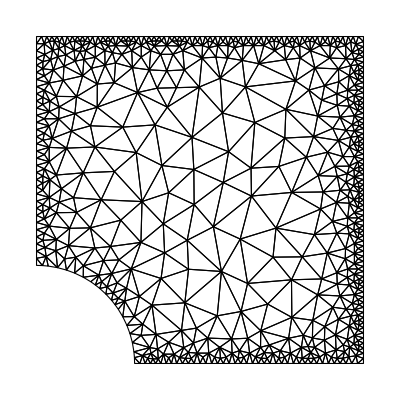

{1227,1593}

{852,1593}

{1227,1936}

```mathematica
Needs["NDSolve`FEM`"]
order=2;
mesh=ToElementMesh[ImplicitRegion[300<=Sqrt[x x+ y y],{x,y}],{{0,1000},{0,1000}},MaxCellMeasure->8000,"MaxBoundaryCellMeasure"->30,"MeshOrder"->order,"NodeReordering"->True]
mesh["Wireframe"]
topol=mesh["MeshElements"][[1,1]];
nnodes=mesh["Coordinates"];
nodetofind={{300,0},{0,300}};
{hole1,hole2}=FindIds[nnodes,nodetofind]
nodetofind={{300,0},{1000,0}};
{inferiorline1,inferiorline2}=FindIds[nnodes,nodetofind]
nodetofind={{0,300},{0,1000}};
{leftline1,leftline2}=FindIds[nnodes,nodetofind]
```

```mathematica
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,order 3}];
eltype=2;
forcing=0.;
young=205000;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
{KE,FE}=Assemble[allcoords,nnodes,topol,order,eltype];
matrix=MatrixPlot[KE,ImageSize->Large]
```

-Graphics-

5998.69

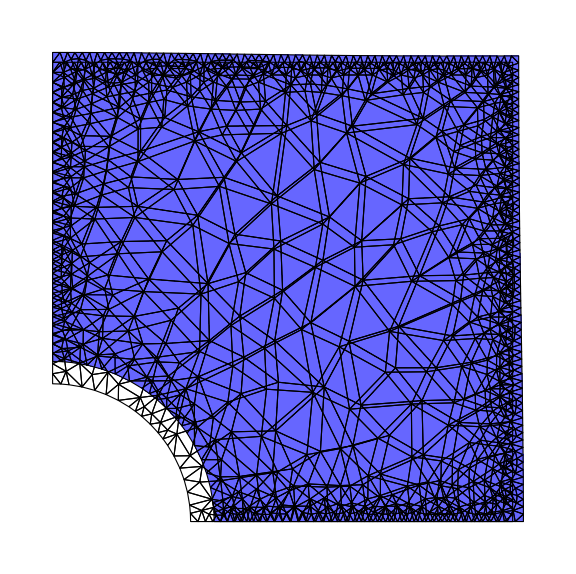

```mathematica
FE=Table[0,{Length[KE]}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,inferiorline1,inferiorline2,{{1,1},{1,10^12}},{0,0},order];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,leftline1,leftline2,{{10^12,1},{1,1}},{0,0},order];
f[pt_]:=-10;
FE=ContributeLineNewman[FE,f,nnodes,order,hole1,hole2];
Sum[FE[[i]],{i,1,Length[FE]}]
sol=LinearSolve[KE,FE,Method->"Banded"];
scale=2302;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVis1=Graphics[{FaceForm[],EdgeForm[{Dashing[Tiny],Thick}],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3}]]]]}];
meshVisDef=Graphics[{FaceForm[{Blue,Opacity[0.6]}],EdgeForm[Black],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3}]]]]}];
defplussundef=Show[meshVisDef,meshVis1,ImageSize->Large]
```

```mathematica
{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol,eltype]//Simplify//Chop;
stress=ComputeStress[(dsols),young,nu][[1]];
```

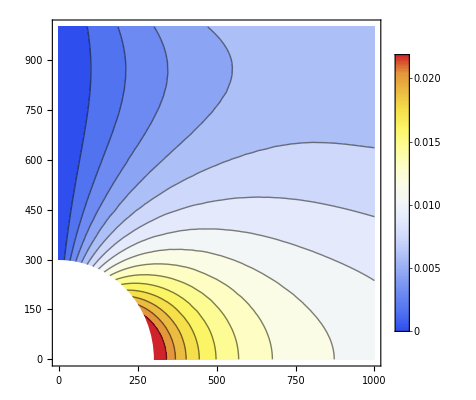

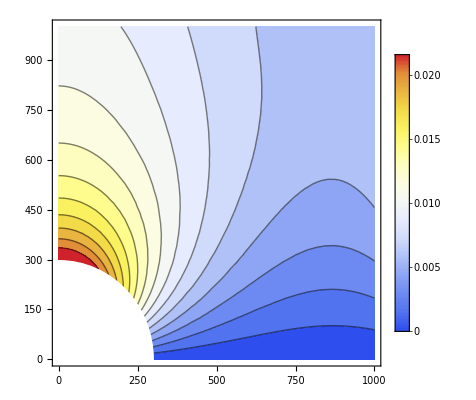

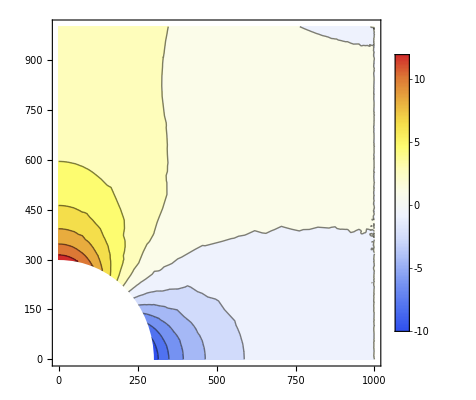

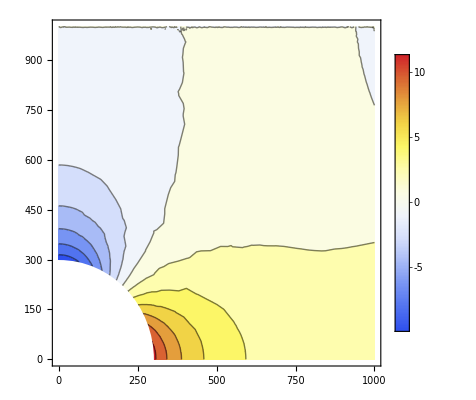

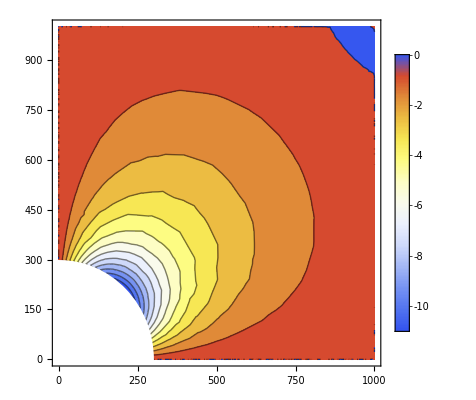

```mathematica
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
tabux=computesollist[X,sols,1];
tabuy=computesollist[X,sols,2];
tabsx=computesollist[X,stress,1];
tabsy=computesollist[X,stress,2];
tabsxy=computesollist[X,stress,3];
lpux=ListContourPlot[Flatten[tabux,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15];
lpuy=ListContourPlot[Flatten[tabuy,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15];
lpsx=ListContourPlot[Flatten[tabsx,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->{-15,15}];
lpsy=ListContourPlot[Flatten[tabsy,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->{-15,15}];
lpsxy=ListContourPlot[Flatten[tabsxy,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->{-12,2}];
Show[lpux,lpd]
Show[lpuy,lpd]
Show[lpsx,lpd]
Show[lpsy,lpd]
Show[lpsxy,lpd]
```

ElementMesh[{{0.,8.},{0.,8.}},{TriangleElement[<737>]}]

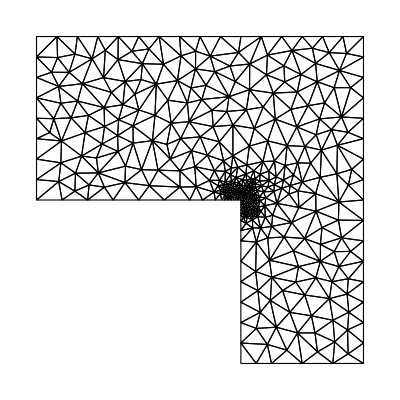

{1133,1493}

{261,1493}

{261,310}

{678,1351}

```mathematica
order=2;
mesh=ToElementMesh[DiscretizeGraphics[GraphicsComplex[{{0,4},{5,4},{5,0},{8,0},{8,8},{0,8}},Polygon[{1,2,3,4,5,6}]]],"MeshOrder"->order,"NodeReordering"->True,MeshRefinementFunction->Function[{vertices,area},Block[{x,y},{x,y}=Mean[vertices];If[x>4.6 && x<5.4&&y>3.6 && y<4.4,area>0.004,area>0.8]]]]
mesh["Wireframe"]
topol=mesh["MeshElements"][[1,1]];
nnodes=mesh["Coordinates"];
nodetofind={{0,4},{5,4}};
{line1a,line1b}=FindIds[nnodes,nodetofind]
nodetofind={{5,4},{5,0}};
{line2a,line2b}=FindIds[nnodes,nodetofind]
nodetofind={{5,0},{8,0}};
{line3a,line3b}=FindIds[nnodes,nodetofind]
nodetofind={{5,8},{8,8}};
{line4a,line4b}=FindIds[nnodes,nodetofind]
```

```mathematica
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,6}];
eltype=2;
forcing=0.;
young=3 10^7;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
{KE,FE}=Assemble[allcoords,nnodes,topol,order,eltype];
matrix=MatrixPlot[KE,ImageSize->Large]
```

-Graphics-

-139.812

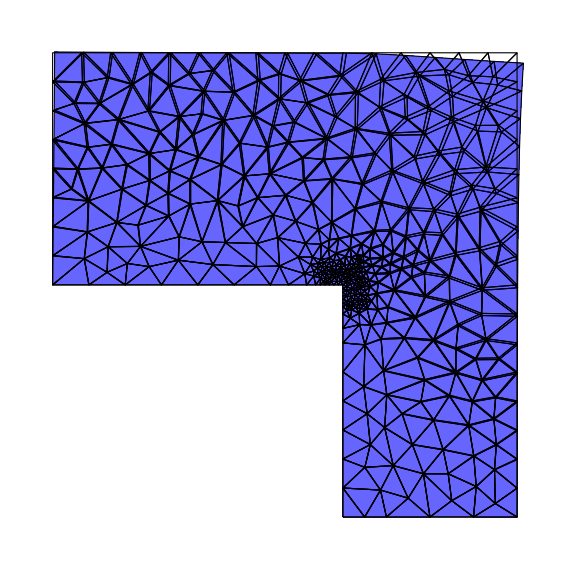

```mathematica
FE=Table[0,{Length[KE]}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,line1a,line1b,{{10^12,1},{1,10^12}},{0,0},order];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,line2a,line2b,{{10^12,1},{1,10^12}},{0,0},order];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,line3a,line3b,{{10^12,1},{1,10^12}},{0,0},order];
c=3;
po=-200;
f[pt_]:=po Sin[Pi pt[[1]]/(2 c)];
FE=ContributeLineNewman[FE,f,nnodes,order,line4a,line4b];
Sum[FE[[i]],{i,1,Length[FE]}]
sol=LinearSolve[KE,FE,Method->"Banded"];
scale=7500;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVis1=Graphics[{FaceForm[],EdgeForm[{Dashing[Tiny],Thick}],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3}]]]]}];
meshVisDef=Graphics[{FaceForm[{Blue,Opacity[0.6]}],EdgeForm[Black],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3}]]]]}];
defplussundef=Show[meshVisDef,meshVis1,ImageSize->Large]
```

```mathematica
Max[sol]
Min[sol]
```

0.0000145108

-0.0000238346

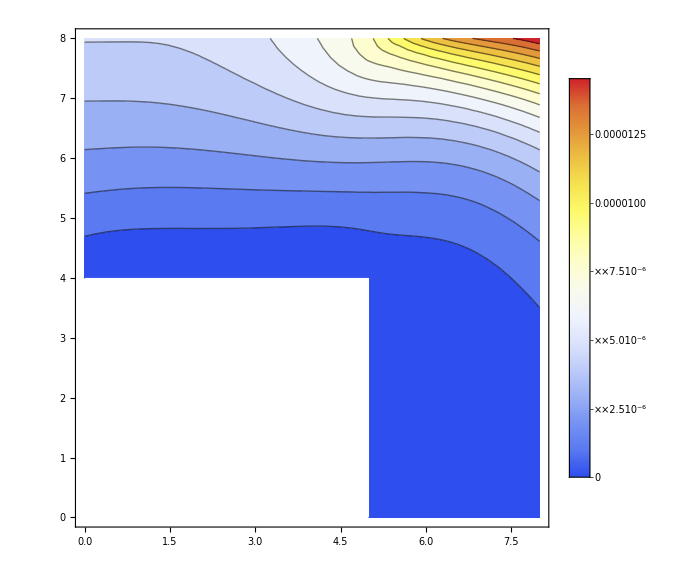

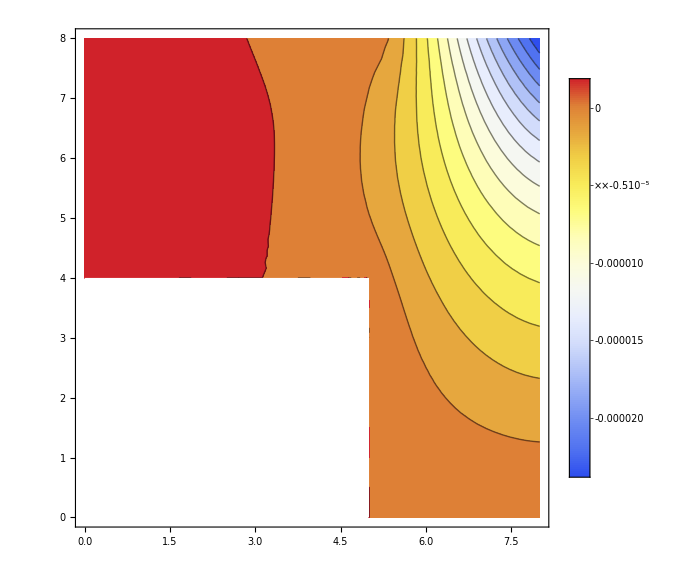

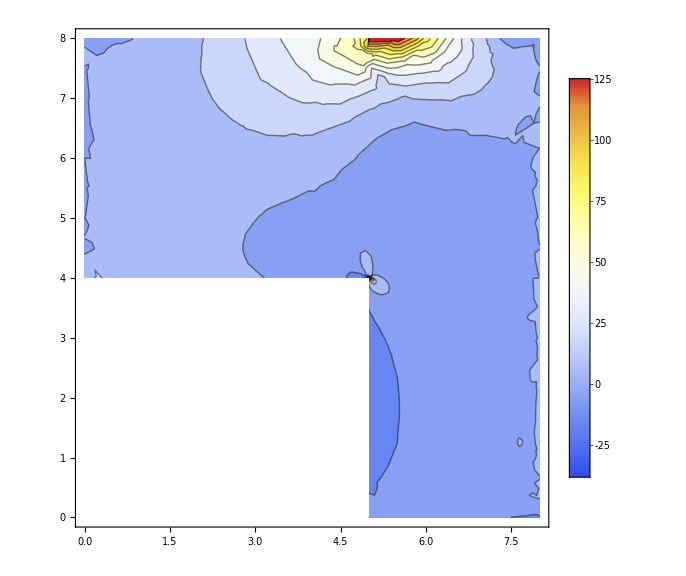

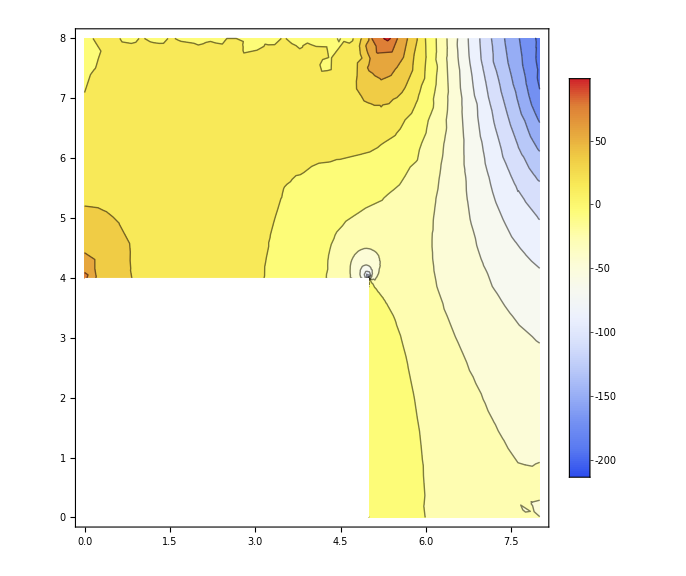

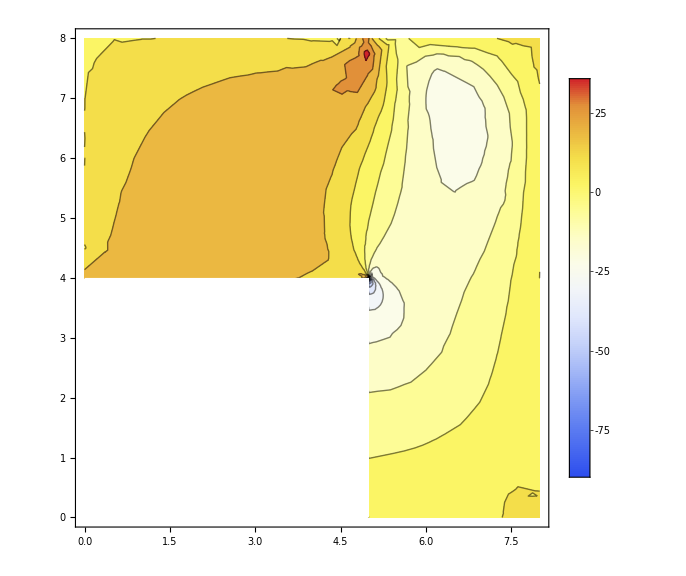

```mathematica
{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol,eltype]//Simplify//Chop;
stress=ComputeStress[(dsols),young,nu][[1]];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
tabux=computesollist[X,sols,1];
tabuy=computesollist[X,sols,2];
tabsx=computesollist[X,stress,1];
tabsy=computesollist[X,stress,2];
tabsxy=computesollist[X,stress,3];
lpux=ListContourPlot[Flatten[tabux,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->Large];
lpuy=ListContourPlot[Flatten[tabuy,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->Large];
lpsx=ListContourPlot[Flatten[tabsx,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->Large];
lpsy=ListContourPlot[Flatten[tabsy,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->Large];
lpsxy=ListContourPlot[Flatten[tabsxy,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->Large];
Show[lpux,lpd]
Show[lpuy,lpd]
Show[lpsx,lpd]
Show[lpsy,lpd]
Show[lpsxy,lpd]
```